```mathematica
(*
JK-Bianchi-Fundamental-Domain.m;
Describe a Fundamental Domain of a Bianchi group by its vertices in the upper-half space model
1. In Mathematica, open and run this file after specifying the value of d. (default value: d = 29);
*)
(* Need: magma at Applications/Magma/ *)
(* Need: Aurel Page's package in the notebook directory *)
```

```mathematica
IterateMax=10000;
(* Specify the value of d, for Γ=PSL(2,Sqrt[-d]) *)
(* Class number one cases = -d where d is one of
1, 2, 3, 7, 11, 19, 43, 67, 163 *)
d=43;
(*  refPoint = 1/3-1/2 i + 17/5 j, by Page's choice *)
RefPoint = {1/3,-1/2,17/5};
Needs["Quaternions`"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* z+rj-based isometric sphere  Returns A when the circle/line is given by {{z} 1} { {a b},{\bar{b} c} } {\bar{z},{1}} 
CONVENTION: ((a B) (\bar B c) );
See Lemma in the draft;
*)
IsomSphere[g_List,z_,r_]:=
Module[{a,b,c,d,m,n,U,V,W,R,M},
If[!MatrixQ[g],Return[False]];
m=Length[g];n=Length[Transpose[g]];
If[(m-2)^2+(n-2)^2>0, Return[False]];
If[Det[g]!=1,Return[False]];
M={{r^(1/2),z/r^(1/2)},{0,r^(-1/2)}};
{{a,b},{c,d}}=Inverse[M].g.M;
R=Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2;
U=b Conjugate[a]+d Conjugate[c];
V=Abs[a]^2+Abs[c]^2-1;
W=Abs[U]^2+V^2-(R-2);
Return[Simplify[{{1,0},{-Conjugate[z],1}}.{{W,r (R-2)U},{r (R-2)Conjugate[U],r^2(W-2V(R-2)+(R-2)^2)}}.{{1,-z},{0,1}}]]
];
IsomSphereRef[g_List]:=IsomSphere[g,RefPoint[[1]]+RefPoint[[2]]I,RefPoint[[3]]];

(* from a 2x2 matrix ( (a b) (bar b c) ) representing a circle to its Euclidean center and radius on \bC *)
CircleMatrixToEuclidean[mat_List]:=
Module[{a,b,bb,c,s,t},
If[Dimensions[mat]!={2,2}, Return[False]];
{{a,b},{bb,c}}=mat;
If[(a==b==0) || bb!=Conjugate[b]||!Element[c,Reals], Return[False]];

(* If mat is a line, return {0, a point on the line (the foot of the perpendicular from the origin if the line does not pass the origin),  a normal vector≠0};
In other words, for the output (0,c0,r0), the line passes through c0 and c0+I r0;
Return False if c is not real;
*)
(* If mat is a circle, return {1, center, radius} *)
Return[If[a==0,
{0,-c/(2*Conjugate[b]),1/Conjugate[b]},{1,-b/a,Sqrt[Abs[b]^2/a^2-c/a]}]];
];

(* Generate the n-dimensional standard basis vector e_i = (0,...,1,0,..,0) *)
stdvec[i_Integer,n_Integer]:=
Module[{l},
If[n<=0||i<0||i>n,Return[False]];
l=Table[0,n];
If[i!=0,l=
ReplacePart[l,i->1]];
Return[l];
];


(* Note.
#Faces of FD = #Basis of Bianchi = #dimsrc

Need for the next paragraph:
JK-Bianchi-FD-out-N-H1-gen.txt
JK-Bianchi-FD-out-Edges.txt
JK-Bianchi-FD-out-Faces.txt
JK-Bianchi-FD-out-psl-matrices.txt
JK-Bianchi-FD-out-quotients.txt

*)
(* Decide if two points x,y in R3 are weakly separated by the ``hemisphere'' given as
 sph = {signature,center,radius}, which is;
			signature = 1 => hemisphere with (center c0 in \bC, radius r0);
			signature = 0 => vertical plane containing the line joining c0 and c0+r0 I;

Returns;
	false if something is wrong;
	1 if  separating;
	-1 if if one of the points is on the sphere;
	0 if nonseparated;
*)
IsSeparating[x_List,y_List,sph_List]:=
Module[
{flag,sig,c0,r0,t,x0,y0,c1},
If[Dimensions[{x,y,sph}]!={3,3},Return[False]];
{sig,c0,r0}=sph;
c1={Re[c0],Im[c0],0};
If[sig==1,
If[Dimensions[c1]!={3}||!Element[r0,Reals]||r0≤0,Return[False]];
t=(Norm[x-c1]^2-r0^2)(Norm[y-c1]^2-r0^2);
Return[If[t<0,1,If[t==0,-1,0]]];
];
(* If sig==0, then the vertical plane passes through c0 and c0+ r0 I;
x0 and y0 are the projections of x and y onto C;
They are on the same side or not, depending on the signature of Re[(x0-c0)(y0-c0) conj(r0)^2];
*)
If[sig==0,
x0=Complex[x[[1]],x[[2]]];y0=Complex[y[[1]],y[[2]]];
t=Re[(x0-c0)Conjugate[r0]]Re[(y0-c0)Conjugate[r0]]//N;
Return[If[t<0,1,If[t==0,-1,0]]];
];
];

(* PSL(2,C) action on a point in the upper half space *)
PSLH3[g_List,p_List]:=Module[{g1,g2,g3,g4,p1,p2,p3,q,qp},
If[Dimensions[g]!={2,2}||Dimensions[p]!={3},Return[False]];
{{g1,g2},{g3,g4}}=g;
{p1,p2,p3}=p;
q=Divide[Quaternion[Re[g1],Im[g1],0,0]**Quaternion[p1,p2,p3,0]+Quaternion[Re[g2],Im[g2],0,0],
Quaternion[Re[g3],Im[g3],0,0]**Quaternion[p1,p2,p3,0]+Quaternion[Re[g4],Im[g4],0,0]];
Return[Drop[List@@q,-1]];
];


(* Starting from q, apply elements from a list lg of isometries to obtain a point qp that is in the same chamber as the RefPoint;
p_List is not used -- needs a correction later *)
(* See Lemma {l:reflect} *)
ReflectH3[p_List,q_List,lg_List]:=Module[{lgl,i,syseq,ltemp,qp,count,j,ltemp3},
lgl=Length[lg];
syseq={};
For[i=1,i<=lgl,i++,
AppendTo[syseq,ComplexExpand[CircleMatrixToEuclidean[IsomSphereRef[lg[[i]]]]]]
];
ltemp={};
count=0;
qp=q;
For[i=1,i<=lgl,i++,
If[count++>IterateMax,Print["Overflow"];Break[]];
If[IsSeparating[RefPoint,qp,syseq[[i]]]==1,
ltemp3={};
For[j=1,j<=lgl,j++,
AppendTo[ltemp3,IsSeparating[RefPoint,qp,syseq[[j]]]]];
Print["The indices of separating hyps = ",Position[ltemp3,1], " and we now apply g[",i,"] = ",lg[[i]]//MatrixForm," to qp = ",qp];
qp=PSLH3[lg[[i]],qp];
AppendTo[ltemp,lg[[i]]];
i=1;Continue[];
];

];
ltemp3={};
For[j=1,j<=lgl,j++,
AppendTo[ltemp3,IsSeparating[RefPoint,qp,syseq[[j]]]]];
Print["Final score: ",ltemp3];
Return[{ltemp,qp}];
];
```

```mathematica
strtmp="d := "<>ToString[d]<>";";
Export["JK-Bianchi-FD-initial.txt",strtmp];
Run["/Applications/Magma/magma JK-Bianchi-FD-initial.txt JK-Bianchi-FD-rev5.m"];dimtar=ToExpression[Import["./JK-Bianchi-FD-out-N-H1-gen.txt"]];

(* Combinatorial data of the fundamental polyhedron *)
(* Neighboring faces for each edge*)
str=Import["./JK-Bianchi-FD-out-Edges-nbfaces.txt"];
ledgesNBfaces = ToExpression[str];

(* Neighboring edges for each face*)
str=Import["./JK-Bianchi-FD-out-Faces-nbedges.txt"];
lfacesNBedges = ToExpression[str];

(* Number of edges, faces and vertices *)
eno=Length[ledgesNBfaces];
fno=Length[lfacesNBedges];
vno=2+eno-fno;

(* List of the vertices of the FD, numerically computed *)
str=Import["./JK-Bianchi-FD-out-Edges.txt"];
str=StringDelete[str,"\\\n"];
str=StringReplace[str,"E"~~a:DigitCharacter~~b:DigitCharacter~~c:DigitCharacter:>"*10^("~~a~~b~~c~~")"];
str=StringReplace[str,"E-"~~a:DigitCharacter~~b:DigitCharacter~~c:DigitCharacter:>"*10^(-"~~a~~b~~c~~")"];
str=StringReplace[str,"E"~~a:DigitCharacter~~b:DigitCharacter:>"*10^("~~a~~b~~")"];
str=StringReplace[str,"E-"~~a:DigitCharacter~~b:DigitCharacter:>"*10^(-"~~a~~b~~")"];
str=StringReplace[str,"E"~~a:DigitCharacter:>"*10^("~~a~~")"];
str=StringReplace[str,"E-"~~a:DigitCharacter:>"*10^(-"~~a~~")"];

(* List of edges, in the form of (center, radius, axis1, axis2, axis3, angle-start, angle-end} *)
str=StringReplace[str,{"i"->"ToQuaternion[I]","j"->"ToQuaternion[J]","k"->"ToQuaternion[K]"}];
ledges=ToExpression[str];
lvertices={};
lcusps={};
Clear[p];
For[i=1,i<=Length[ledges],i++,
If[Length[ledges[[i]]]==7,
{c,r,e1,e2,e3,a1,a2}=ledges[[i]]];

p[1]=c+r*e1*Cos[a1]+r*e2*Sin[a1];
p[2]=c+r*e1*Cos[a2]+r*e2*Sin[a2];

templist={i};

j=1;
flagcusp=False;
{x,y,z}=Drop[List@@p[j],-1];
r=x^2+y^2+z^2;
If[r≥1,Print["The initial vertex of the ",i," th edge is a cusp"];lcusps=Append[lcusps,{i,1,x,y,z}];flagcusp=True;
templist=Append[templist,{0,0,Infinity}];
];
If[!flagcusp,
q=Divide[p[j]+ToQuaternion[J],1+ToQuaternion[J]**p[j]];
(* xyz coordinate of the starting i=1 or ending i=2 point of an edge for the upper-halfspace model *)
qp=Drop[List@@q,-1];
templist=Append[templist,qp];
];

j=2;
flagcusp=False;
{x,y,z}=Drop[List@@p[j],-1];
r=x^2+y^2+z^2;
If[r≥1,Print["The terminal vertex of the ",i," th edge is a cusp"];lcusps=Append[lcusps,{i,2,x,y,z}];flagcusp=True;
templist=Append[templist,{0,0,Infinity}];
];
If[!flagcusp,
q=Divide[p[j]+ToQuaternion[J],1+ToQuaternion[J]**p[j]];
(* xyz coordinate of the starting i=1 or ending i=2 point of an edge for the upper-halfspace model *)
qp=Drop[List@@q,-1];
templist=Append[templist,qp];
];


lvertices=Append[lvertices,templist];

];
lvertices=Union[Drop[Transpose[lvertices],1][[1]],Drop[Transpose[lvertices],1][[2]]];
lvertices=SetAccuracy[lvertices,5];
Print[ListPointPlot3D[lvertices]];
lcusps=Transpose[lcusps][[1]];

(* List of the faces of the FD *)
str=Import["./JK-Bianchi-FD-out-Faces.txt"];
str=StringDelete[str,"\\\n"];
str=StringReplace[str,{"i"->"ToQuaternion[I]","j"->"ToQuaternion[J]","k"->"ToQuaternion[K]"}];
(* The list of the Euclidean center, radius, edges of the faces in the ball model *)
lfaces=ToExpression[str];
lfaceedges={};

For[i=1,i<=Length[lfaces],i++,
c=Drop[List@@lfaces[[i]][[1]],-1];
r=lfaces[[i]][[2]];
lfaceedges=Append[lfaceedges,{c,r,lfaces[[i]][[3]]}];
];



str=Import["./JK-Bianchi-FD-out-psl-matrices.txt"];
str=StringReplace[str,{"alpha"->"Sqrt[-d]"}];

lgen=ToExpression[str];
lfacesPSL=lgen;
dimsrc=Length[lgen];
realtracelist={};
For[i=1,i<=dimsrc,i++,
mattmp=lgen[[i]];
If[Im[Tr[mattmp]]==0,
lgen=ReplacePart[Append[lgen,mattmp],{i->{{0,0},{0,0}}}];
realtracelist=Append[realtracelist,i];
];
]
str1=Import["./JK-Bianchi-FD-out-quotients.txt"];
str2="{"<>StringReplace[str1,{"\n"->",", "HPG."->"vec"}]<>"}";
l=ToExpression[str2];
veclist=
Table["vec"<>ToString[i],{i,1,dimtar}];
For[i=1,i<=dimtar,i++,
MakeExpression@veclist[[i]]/. _@x_:>(x=stdvec[i,dimtar]);
];
For[i=1,i<=Length[realtracelist],i++,
l=Append[l,l[[realtracelist[[i]]]]];
l=ReplacePart[l,realtracelist[[i]]->0];
]
m={};
genlist={};
For[i=1,i<=Length[l],i++,
If[l[[i]]==0,Continue[]];
rkcurr=Length[m];
mtmp=Append[m,l[[i]]];
If[MatrixRank[mtmp]>rkcurr,m=mtmp;genlist=Append[genlist,i]];
If[Length[m]==dimtar,Break[]];
];
Print["generators needed to span H1"];
For[i=1,i<=Length[genlist],i++,
Print[lgen[[genlist[[i]]]]//MatrixForm];
];
Export["JK-Bianchi-FD-out-gen-psl-matrices.txt",lgen[[genlist]]];


(* List of parabolic face-pairing generators: They fix infinity *)
lfacesParabolic={};
For[i=1,i<=fno, i++,
If[Abs[Tr[lfacesPSL[[i]]]]==2,
lfacesParabolic=Append[lfacesParabolic,i];
]];
Print["The list of cusp vertices is : ",lcusps];

lfacesIncidenceMatrix={};
For[i=1,i<=fno,i++,
temp = Table[0, eno];
temp = ReplacePart[temp,Partition[lfacesNBedges[[i]],1]-> 1];
lfacesIncidenceMatrix=Append[lfacesIncidenceMatrix,temp];
];
lfacesAdjacencyMatrix=lfacesIncidenceMatrix.Transpose[lfacesIncidenceMatrix];
lfacesAdjacency={};
For[i=1,i<=fno,i++,
temp=lfacesAdjacencyMatrix[[i]];
lfacesAdjacency=Append[lfacesAdjacency,Flatten[Position[temp,1]]];
];
(* Make a list i = 1..fno such consisting of
{i: face index, g: face pairing PSL(2,C), {{W,U},{Conjugate[U],V}}: isometric sphere equation of g = face equation of face i, {e1,e2,...}: neighboring face indices};
*)

(* The {a,B},{\bar B, c}} symbolic expression for each face, which is the isometric sphere of the corresponding element *)
IsomSphereList={};

For[i=1,i<=fno,i++,
IsomSphereList=Append[IsomSphereList,{i,lfacesPSL[[i]], IsomSphereRef[lfacesPSL[[i]]], lfacesAdjacency[[i]]}];
];


(* Define the fundamental domain region *)
sys={};
For[i=1,i<=fno,i++,
AppendTo[sys,{s0,c0,r0}=CircleMatrixToEuclidean[IsomSphereList[[i]][[3]]];
a0=Re[c0];b0=Im[c0];aa0=Re[r0];bb0=Im[r0];
If[s0==1,
((xx-a0)^2+(yy-b0)^2+zz^2-r0^2)>0,((xx-a0)aa0+(yy-b0)bb0)((1/3-a0)aa0+(-1/2-b0)bb0)>0]];
];
AppendTo[sys,zz>0];
reg= ImplicitRegion[Resolve[sys,Reals],{xx,yy,zz}];
MM=3;
sys2=Join[sys,{0<zz<MM}];
reg2= ImplicitRegion[Resolve[sys2,Reals],{xx,yy,zz}];
linv={};
For[i=1,i<=fno,i++,
m1=lfacesPSL[[i]];
For[j=i,j<=fno,j++,
m2=lfacesPSL[[j]];
If[m1.m2==IdentityMatrix[2],
AppendTo[linv,{i,j}];
If[i==j,Print["Coincide at i = j = ",i]]];
]];
Print["The pairs of inverse faces are ",linv];
```

The initial vertex of the 3 th edge is a cusp

The initial vertex of the 4 th edge is a cusp

The terminal vertex of the 5 th edge is a cusp

The initial vertex of the 6 th edge is a cusp

The terminal vertex of the 7 th edge is a cusp

The initial vertex of the 8 th edge is a cusp

-Graphics3D-

generators needed to span H1

(1/2 (-1-ⅈ √43) | 4
-3 | 1/2 (1-ⅈ √43))

(1/2 (-1-ⅈ √43) | 7
3 | -1+ⅈ √43)

The list of cusp vertices is : {3,4,5,6,7,8}

The pairs of inverse faces are {{2,5},{3,27},{4,8},{6,9},{7,11},{10,13},{12,21},{14,15},{17,19},{18,20},{22,23},{25,26},{29,30},{31,42},{32,33},{34,35},{36,37},{38,39},{40,41},{45,46}}

Ref point = {0.333333,-0.5,3.4}

Separated by i = 35

The indices of separating hyps = {{35},{41}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.2,1.2,0.001} for the circle {0.,0.833333,-11.56}

Separated by i = 5

The indices of separating hyps = {{5},{10},{26},{38},{41},{44},{45}} and we now apply g[5] = (1/2 (1-ⅈ √43) | -4
3 | 1/2 (-1-ⅈ √43)) to qp = {0.2,1.2,0.001} for the circle {1.,0.163535+1.11344 ⅈ,0.363422}

Separated by i = 32

The indices of separating hyps = {{32},{43}} and we now apply g[32] = (1 | -1
1 | 0) to qp = {-0.127719,-0.147103,0.00883156} for the circle {1.,0.0296179,0.985525}

Separated by i = 35

The indices of separating hyps = {{35},{39},{40}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {4.35841,-3.86815,0.23223} for the circle {0.,0.833333,-11.56}

Separated by i = 35

The indices of separating hyps = {{35},{39},{40}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {3.35841,-3.86815,0.23223} for the circle {0.,0.833333,-11.56}

Separated by i = 35

The indices of separating hyps = {{35},{39},{40}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {2.35841,-3.86815,0.23223} for the circle {0.,0.833333,-11.56}

Separated by i = 35

The indices of separating hyps = {{35},{39},{40}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.35841,-3.86815,0.23223} for the circle {0.,0.833333,-11.56}

Separated by i = 39

The indices of separating hyps = {{39},{40}} and we now apply g[39] = (-1 | 1/2 (1-ⅈ √43)
0 | -1) to qp = {0.358415,-3.86815,0.23223} for the circle {0.,0.332092-2.17767 ⅈ,-0.0477686+0.31324 ⅈ}

Separated by i = 32

The indices of separating hyps = {{32},{43}} and we now apply g[32] = (1 | -1
1 | 0) to qp = {-0.141585,-0.589426,0.23223} for the circle {1.,0.0296179,0.985525}

Separated by i = 35

The indices of separating hyps = {{35}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.33599,-1.39873,0.551091} for the circle {0.,0.833333,-11.56}

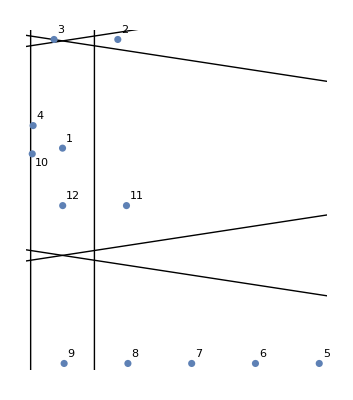

The indices of separating hyps = {{35}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {0.897508,-0.92302,0.450151} for the circle {0.,0.833333,-11.56}

Separated by i = 35

The indices of separating hyps = {{32},{43}} and we now apply g[32] = (1 | -1
1 | 0) to qp = {0.0962275,-0.866599,0.422635} for the circle {1.,0.0296179,0.985525}

Separated by i = 32

The indices of separating hyps = {{5},{38},{41}} and we now apply g[5] = (1/2 (1-ⅈ √43) | -4
3 | 1/2 (-1-ⅈ √43)) to qp = {0.2,1.2,0.2} for the circle {1.,0.163535+1.11344 ⅈ,0.363422}

Separated by i = 5

The indices of separating hyps = {{35},{41}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.2,1.2,0.2} for the circle {0.,0.833333,-11.56}

Separated by i = 35

Ref point = {0.333333,-0.5,3.4}

Ref point = {0.333333,-0.5,3.4}

Separated by i = 35

The indices of separating hyps = {{35},{41}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.2,1.2,0.02} for the circle {0.,0.833333,-11.56}

Separated by i = 5

The indices of separating hyps = {{5},{10},{26},{38},{41},{44},{45}} and we now apply g[5] = (1/2 (1-ⅈ √43) | -4
3 | 1/2 (-1-ⅈ √43)) to qp = {0.2,1.2,0.02} for the circle {1.,0.163535+1.11344 ⅈ,0.363422}

Separated by i = 32

The indices of separating hyps = {{32},{43}} and we now apply g[32] = (1 | -1
1 | 0) to qp = {-0.118669,-0.176177,0.171202} for the circle {1.,0.0296179,0.985525}

Separated by i = 35

The indices of separating hyps = {{35},{39}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {2.59436,-2.36699,2.30015} for the circle {0.,0.833333,-11.56}

Separated by i = 35

The indices of separating hyps = {{35},{39}} and we now apply g[35] = (1 | -1
0 | 1) to qp = {1.59436,-2.36699,2.30015} for the circle {0.,0.833333,-11.56}

Separated by i = 39

The indices of separating hyps = {{39},{40}} and we now apply g[39] = (-1 | 1/2 (1-ⅈ √43)
0 | -1) to qp = {0.594362,-2.36699,2.30015} for the circle {0.,0.332092-2.17767 ⅈ,-0.0477686+0.31324 ⅈ}

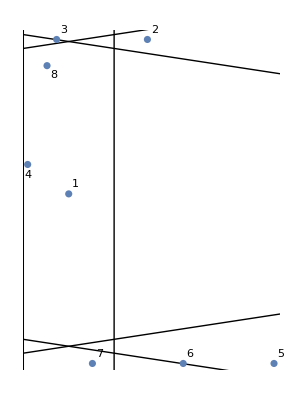

```mathematica
lg=lfacesPSL;
p=RefPoint;
q={1.2,1.2,.001};
Print["Ref point = ",p//N];
lgl=Length[lg];
syseq={};
For[i=1,i<=lgl,i++,
AppendTo[syseq,ComplexExpand[CircleMatrixToEuclidean[IsomSphere[lg[[i]],p[[1]]+p[[2]]I,p[[3]]]]]]
];
ltemp={};
lq={};
count=0;
qp=q;
lq={p,qp};
For[i=1,i<=lgl,i++,
If[count++>1000,Print["Overflow"];Break[]];
If[IsSeparating[p,qp,syseq[[i]]]==1,
Print["Separated by i = ",i];
ltemp3={};
For[j=1,j<=lgl,j++,
AppendTo[ltemp3,IsSeparating[p,qp,syseq[[j]]]]];
Print["The indices of separating hyps = ",Position[ltemp3,1], " and we now apply g[",i,"] = ",lg[[i]]//MatrixForm," to qp = ",qp," for the circle ",syseq[[i]]//N];
qp=PSLH3[lg[[i]],qp];
AppendTo[ltemp,lg[[i]]];
AppendTo[lq,qp];
i=1;Continue[];
];
];

lq2=Transpose[Take[Transpose[lq],2]];
lq2Label=Table[Labeled[lq2[[i]],i],{i,Length[lq2]}];

lgr={};
For[i=1,i<=lgl,i++,
{s1,c1,r1}=syseq[[i]];
If[s1==1,Continue[]];
x1=Re[c1];y1=Im[c1];v1=-Im[r1];v2=Re[r1];
gr=InfiniteLine[{{x1,y1},{x1+v1,y1+v2}}];
AppendTo[lgr,gr];];
MB=2.5;
Show[{Graphics[Table[{lgr[[i]]},{i,1,Length[lgr]}]],ListPlot[lq2Label]}]
```

```mathematica
Print[p,",",qp];
```

{1/3,-1/2,17/5},{0.5,-1.84872,0.000015}

```mathematica
Print[RegionPlot3D[reg2,PlotStyle->Directive[Opacity[0.5],Pink,Specularity[White,20]],PlotPoints->60,Mesh->5]];
```

-Graphics3D-

```mathematica
Print["The volume of the fundamental polyhedron at d = ",d," is ",NIntegrate[1./zz^3,{xx,yy,zz}∈reg]];
```

```mathematica
MM=2.;sys3={1/2 (1/2-xx)>0,1/2 (1/2+xx)>0,1/4 (1/4+xx)+1/4 √43 ((√43)/4+yy)>0,1/4 (1/4-xx)-1/4 √43 (-(√43)/4+yy)>0,1/4 (1/4+xx)-1/4 √43 (-(√43)/4+yy)>0,1/4 (1/4-xx)+1/4 √43 ((√43)/4+yy)>0};reg3= ImplicitRegion[sys3,{{xx,-MM,MM},{yy,-MM,MM}}];
RegionPlot[reg3,PlotStyle->Directive[Opacity[0.5],Pink,Specularity[White,20]],PlotPoints->Automatic,Mesh->5]
```

-Graphics-

```mathematica
discOd[d_Integer]:=Return[If[Mod[d,4]==3,d,4d]];LobachevskyLambda[x_Real]:=1/4 ⅈ (PolyLog[2,ⅇ^(-2ⅈ x)]-PolyLog[2,ⅇ^(2ⅈ x)]);
d=43;
DD=discOd[d];
Print[vol=Re[DD/12 * Sum[JacobiSymbol[-DD,k]LobachevskyLambda[Pi k/DD],{k,0,DD-1}]//N]];
```

8.11299